```mathematica
Quit[];
```

```mathematica
1+1//Timing
```

{6.×10^-6,2}

```mathematica
<<"/Users/noahsteinberg/Library/Mathematica/Applications/DsixTools/DsixTools.m"
```

DsixTools 1.1.3

by Alejandro Celis, Javier Fuentes-Martin, Avelino Vicente and Javier Virto

Reference: arXiv:1704.04504

Website: https://dsixtools.github.io/

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version.

See ?DsixTools`* for a list of routines and variables.

### Options

```mathematica
Options
LOWSCALE=mW;
HIGHSCALE=10^19;
CPV=0;
ReadRGEs=1;
RGEsMethod=1;
ExportRGEs=0;
UseRGEsSM=1;
exportSMEFTrunner=0;
exportEWmatcher=0;
exportWETrunner=0;
inputWCsType=1;

Init[g]=e/Sin[θW];
Init[gp]=e/Cos[θW];
Init[gs]=Sqrt[4Pi(0.1205)]; (*We feed as input to DsixTools Subscript[α, s](Subscript[M, Z])*);

Init[λ]=mh^2/v^2;
Init[m2]=mh^2/2;
Init[GU[1,1]]=1.23231*10^-5;
Init[GU[1,2]]=-1.64215*10^-3;
Init[GU[1,3]]=5.90635*10^-3;
Init[GU[2,1]]=2.84527*10^-6;
Init[GU[2,2]]=7.10724*10^-3;
Init[GU[2,3]]=-4.18547*10^-2;
Init[GU[3,1]]=4.65426*10^-8;
Init[GU[3,2]]=3.08758*10^-4;
Init[GU[3,3]]=0.994858;
Init[GD[1,1]]=2.70195*10^-5;
Init[GD[1,2]]=0;
Init[GD[1,3]]=0;
Init[GD[2,1]]=0;
Init[GD[2,2]]=5.51888*10^-4;
Init[GD[2,3]]=0;
Init[GD[3,1]]=0;
Init[GD[3,2]]=0;
Init[GD[3,3]]=2.403012*10^-2;
Init[GE[1,1]]=2.93766*10^-6;
Init[GE[1,2]]=0;
Init[GE[1,3]]=0;
Init[GE[2,1]]=0;
Init[GE[2,2]]=6.07422*10^-4;
Init[GE[2,3]]=0;
Init[GE[3,1]]=0;
Init[GE[3,2]]=0;
Init[GE[3,3]]=1.02157*10^-2;
Init[θ]=0;
Init[θp]=0;
Init[θs]=0;
```

Options

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Example_IO"];
WriteAndReadInputFiles["Options_program2.dat","WCsInput_program2.dat","SMInput_program2.dat"];
```

SetDirectory::cdir: Cannot set current directory to ../Example_IO.

Input : SMEFT Wilson coefficients

```mathematica
(*Now let's run αS from 10 TeV down to Mtop at 1 loop, using DSixTools*)
LoadModule["SMEFTrunner"]
LoadBetaFunctions;
RunRGEsSMEFT;
param1 = FindParameterSMEFT[gs];
```

SMEFTrunner

DsixTools module for the RGE running of the Standard Model Effective Theory

Loading SMEFT β functions

Running

Running finished!

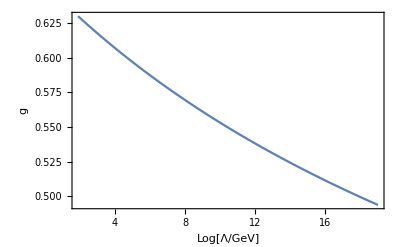
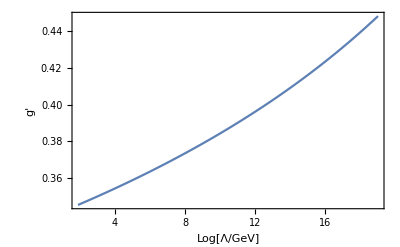
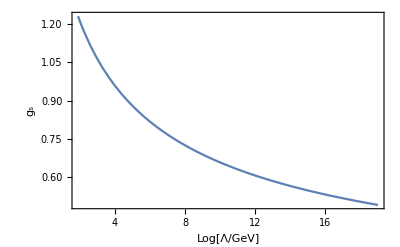

```mathematica
plotGauge1=Plot[outSMEFTrunner[[1]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","g",None,None}];
plotGauge2=Plot[outSMEFTrunner[[2]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","g'",None,None}];
plotGauge3=Plot[outSMEFTrunner[[3]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","g_s",None,None}];
plotGauge={plotGauge1,plotGauge2,plotGauge3}
```

```mathematica
Δλonetwo[x_] := 48 π^2*(1/((25/9)*outSMEFTrunner[[2]]^2) - 1/outSMEFTrunner[[1]]^2)/.t->x
Δλtwothree[x_] := 48 π^2*(-1/outSMEFTrunner[[3]]^2 + 1/outSMEFTrunner[[1]]^2)/.t->x
```

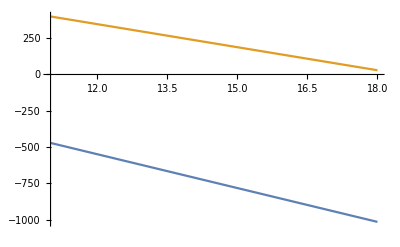

```mathematica
Plot[{Δλonetwo[x],Δλtwothree[x]}, {x,11,18}]
```

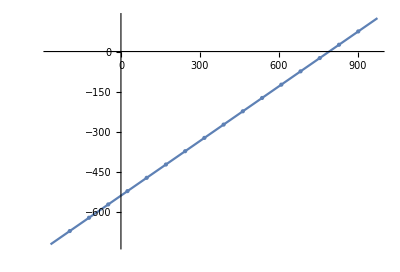

{354.042,276.306,198.571,120.836,43.1004,-34.635,-112.37,-190.106,-267.84}

{-298.522,-351.482,-404.442,-457.402,-510.362,-563.322,-616.281,-669.242,-722.201}

```mathematica
ParametricPlot[{Δλonetwo[x],Δλtwothree[x]},{x,2,18},Mesh->16]
Δλonetwolist = {Δλonetwo[10], Δλonetwo[11], Δλonetwo[12], Δλonetwo[13], Δλonetwo[14], Δλonetwo[15], Δλonetwo[16], Δλonetwo[17], Δλonetwo[18]}
Δλtwothreelist = {Δλtwothree[10], Δλtwothree[11], Δλtwothree[12], Δλtwothree[13], Δλtwothree[14], Δλtwothree[15], Δλtwothree[16], Δλtwothree[17], Δλtwothree[18]}
```

```mathematica
Δλonetwolist
```

{-2919.29,-2809.13,-2698.97,-2588.82,-2478.66,-2368.51,-2258.35,-2148.2,-2038.04}

```mathematica
Δλtwothreelist
```

{2108.34,1917.22,1726.11,1534.99,1343.88,1152.76,961.646,770.53,579.417}

```mathematica
ParametricPlot[{Δλonetwo[x],Δλtwothree[x]},{x,2,18},Mesh->{Subdivide[2,10,18]},MeshStyle->PointSize[Large]];
points=Cases[Normal[pp],Point[x_]:>x,∞];
```